# Efficiency Comparison Physics Data

## Defining Methods and Preamble

## Preamble

```mathematica
(*Set directory paths.*)
SetDirectory[NotebookDirectory[]];
```

## Plotting Method

```mathematica
hexColors={"#3f90da","#ffa90e","#bd1f01","#94a4a2","#832db6","#a96b59","#e76300","#b9ac70","#717581","#92dadd"};
RGBColor/@hexColors
makeBoxCMS[data_,labels_,yLabel_,cmsPos_,tevPos_,precY_:1,xLabelY_:0.06,modelLabel_:"AE", modelLabelPos_:{0.639,0.899}]:=Module[{majorLen,minorLen,makeTicks01,yVals,yTicks,yTicksRight,plot,cmsText,tevText,plotLeft=0.01,plotBottom=0.12,plotWidth=0.98,plotHeight=0.84,xCenters},majorLen=Scaled[0.015];
minorLen=Scaled[0.015/2];
makeTicks01[{vmin_?NumericQ,vmax_?NumericQ},prec_]:=Module[{maj,min},maj=N@FindDivisions[{vmin,vmax},6];
min=N@Flatten@Table[Most@Rest@Subdivide[maj[[k]],maj[[k+1]],6],{k,1,Length[maj]-1}];
Join[({#,NumberForm[#,{6,prec}],{majorLen,0}}&/@maj),({#,"",{minorLen,0}}&/@min)]];
yVals=Flatten[data];
yTicks=makeTicks01[{0,1.05 Max[yVals]},precY];
yTicksRight=yTicks/. {v_,_,len_}:>{v,"",len};


nBoxes=Length[data];
q10=Quantile[#,0.10]&/@data;
q90=Quantile[#,0.90]&/@data;
(*x positions in BoxWhiskerChart coordinates*)
xPos=Range[nBoxes];
     p10p90Graphics=Table[{EdgeForm[None],FaceForm[Directive[RGBColor["#92dadd"],Opacity[0.22]]],Rectangle[{xPos[[i]]-0.39,q10[[i]]},{xPos[[i]]+0.39,q90[[i]]}]},{i,nBoxes}];

plot=BoxWhiskerChart[
data,
{"Outliers",
{"MedianMarker",1.0,Directive[RGBColor["#94a4a2"],AbsoluteThickness[3], Opacity[2]]},
{"Whiskers",Directive[Black,AbsoluteThickness[3]]},
{"Fences",0.5,Directive[Black,AbsoluteThickness[2]]},
{"MeanMarker",0.78,Directive[Black, Opacity[1],AbsoluteThickness[3]]},
{"MeanDiamond",0.8,Directive[RGBColor["#92dadd"], Opacity[0.4]]},
{"Outliers",Graphics[{RGBColor["#3f90da"],Rectangle[{-1,-1},{1,1}]}]}
},
Prolog->p10p90Graphics,
BarSpacing->0.3,
ChartStyle->Table[Directive[RGBColor["#3f90da"],Opacity[0.8]],{Length[data]}],
Frame->True,Axes->False,
FrameTicks->{{yTicks,yTicksRight},{Automatic,Automatic}},
FrameStyle->Directive[Black,AbsoluteThickness[2]],
FrameTicksStyle->Directive[Black,FontSize->22,FontFamily->"TeX Gyre Heros"],
LabelStyle->Directive[Black,FontSize->24,FontFamily->"TeX Gyre Heros"],
FrameLabel->{None,Style[yLabel,Black,FontSize->30,FontFamily->"TeX Gyre Heros"]},
GridLines->{None,Automatic},GridLinesStyle->Directive[GrayLevel[0.85], AbsoluteThickness[1.5]],
ImageSize->1300,AspectRatio->0.65,ImagePadding->{{100,40},{40,40}},PlotRange->{0,1.05 Max[yVals]},
PlotRangePadding->{{Scaled[-0.1],Scaled[-0.03]},{Scaled[0.03],Scaled[0.01]}}
];

cmsText=Row[{Style["CMS",Bold,FontFamily->"TeX Gyre Heros",24],Style[" Simulation Preliminary",Italic,FontFamily->"TeX Gyre Heros",24]}];
tevText=Style["14 TeV",FontFamily->"TeX Gyre Heros",24];
xCenters={0.165, 0.3,0.43, 0.57};

Graphics[
Join[
{
Inset[plot,Scaled[{plotLeft,plotBottom}],{Left,Bottom},Scaled[{plotWidth,plotHeight}]]},
Table[Inset[Style[labels[[i]],FontFamily->"TeX Gyre Heros",22],Scaled[{xCenters[[i]],xLabelY}],{Center,Top}],{i,Length[labels]}],
{
Inset[cmsText,Scaled[cmsPos],{Left,Bottom}],
Inset[tevText,Scaled[tevPos],{Right,Bottom}],
Inset[Framed[Style[modelLabel,FontFamily->"TeX Gyre Heros",Italic,32,Black],Background->White,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],RoundingRadius->0,FrameMargins->{{8,8},{4,4}}],Scaled[modelLabelPos],{Right,Top}]
}],PlotRange->{{0,1},{0,1}},AspectRatio->0.5,ImageSize->1300]]
```

{RGBColor[0.24705882352941178, 0.5647058823529412, 0.8549019607843137],RGBColor[1., 0.6627450980392157, 0.054901960784313725],RGBColor[0.7411764705882353, 0.12156862745098039, 0.00392156862745098],RGBColor[0.5803921568627451, 0.6431372549019608, 0.6352941176470588],RGBColor[0.5137254901960784, 0.17647058823529413, 0.7137254901960784],RGBColor[0.6627450980392157, 0.4196078431372549, 0.34901960784313724],RGBColor[0.9058823529411765, 0.38823529411764707, 0.],RGBColor[0.7254901960784313, 0.6745098039215687, 0.4392156862745098],RGBColor[0.44313725490196076, 0.4588235294117647, 0.5058823529411764],RGBColor[0.5725490196078431, 0.8549019607843137, 0.8666666666666667]}

```mathematica
ClearAll[BootstrapPairedDiffCI,WilcoxonSignedRankPExact,SafeWilcoxonP,CollapsedMethodQ,FormatNum,FormatP,FormatMeanOrDash,FormatAsymPMOrDash,ArchitectureRowDataCompactCollapse,LatexRowCompactAsymCollapse,BuildArchitectureRowsCompactCollapse,BuildLatexTableCompactAsymCollapse];

(*Treat all-zero arrays as collapsed*)
CollapsedMethodQ[x_List]:=AllTrue[x,#==0.&];

(*95% bootstrap CI for paired mean difference:a-b*)
BootstrapPairedDiffCI[a_List,b_List,nBoot_:10000,alpha_:0.05]:=Module[{n,diffs,boots},If[Length[a]=!=Length[b],Return[Missing["LengthMismatch"]]];
n=Length[a];
diffs=a-b;
boots=Table[Mean[RandomChoice[diffs,n]],{nBoot}];
Quantile[boots,{alpha/2,1-alpha/2}]];

(*Exact two-sided Wilcoxon signed-rank p-value*)
WilcoxonSignedRankPExact[a_List,b_List]:=Module[{d,absd,sgn,n,order,sortedAbs,sortedIdx,ranks,groups,start,wPlus,allSums,pLeft,pRight},If[Length[a]=!=Length[b],Return[Missing["LengthMismatch"]]];
d=DeleteCases[a-b,0.];
If[d==={},Return[1.0]];
absd=Abs[d];
sgn=Sign[d];
n=Length[d];
order=Ordering[absd];
sortedAbs=absd[[order]];
sortedIdx=order;
ranks=ConstantArray[0.,n];
groups=Split[Range[n],sortedAbs[[#1]]==sortedAbs[[#2]]&];
start=1;
Do[Module[{len=Length[g],mid},mid=Mean[Range[start,start+len-1]];
ranks[[sortedIdx[[g]]]]=mid;
start+=len;],{g,groups}];
wPlus=Total[Pick[ranks,sgn,1]];
allSums=Total/@(Pick[ranks,#,1]&/@Tuples[{0,1},n]);
pLeft=N[Count[allSums,x_/;x<=wPlus]/Length[allSums]];
pRight=N[Count[allSums,x_/;x>=wPlus]/Length[allSums]];
Min[1.0,2.0 Min[pLeft,pRight]]];

SafeWilcoxonP[a_List,b_List]:=WilcoxonSignedRankPExact[a,b];

FormatNum[x_,digits_:2]:=ToString@NumberForm[x,{Infinity,digits},NumberPadding->{"","0"},NumberPoint->"."];

FormatP[p_]:=Which[MissingQ[p],"-",p<0.001,"<0.001",True,ToString@NumberForm[p,{Infinity,3},NumberPadding->{"","0"},NumberPoint->"."]];

FormatMeanOrDash[x_List,digits_:2]:=If[CollapsedMethodQ[x],"-",FormatNum[Mean[x],digits]];

FormatAsymPMOrDash[center_,ci_List,digits_:2]:=Module[{lower,upper},If[MissingQ[center]||MissingQ[ci],Return["-"]];
lower=center-ci[[1]];
upper=ci[[2]]-center;
"$"<>FormatNum[center,digits]<>"^{+"<>FormatNum[upper,digits]<>"}"<>"_{-"<>FormatNum[lower,digits]<>"}$"];

ArchitectureRowDataCompactCollapse[archName_String,methods_Association,nBoot_:10000,alpha_:0.05]:=Module[{semi,cap,stable,w1,semiCollapsed,capCollapsed,stableCollapsed,w1Collapsed,dCS,dCW,ciCS,ciCW,pCS,pCW},semi=methods["semisupervised"];
cap=methods["CAP"];
stable=methods["stable"];
w1=methods["wasserstein"];
If[!(Length[semi]==Length[cap]==Length[stable]==Length[w1]),Return[<|"Architecture"->archName,"Error"->"All method arrays must have equal lengths."|>]];
semiCollapsed=CollapsedMethodQ[semi];
capCollapsed=CollapsedMethodQ[cap];
stableCollapsed=CollapsedMethodQ[stable];
w1Collapsed=CollapsedMethodQ[w1];
dCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],Mean[cap-stable]];
dCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],Mean[cap-w1]];
ciCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],BootstrapPairedDiffCI[cap,stable,nBoot,alpha]];
ciCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],BootstrapPairedDiffCI[cap,w1,nBoot,alpha]];
pCS=If[capCollapsed||stableCollapsed,Missing["Collapsed"],SafeWilcoxonP[cap,stable]];
pCW=If[capCollapsed||w1Collapsed,Missing["Collapsed"],SafeWilcoxonP[cap,w1]];
<|"Architecture"->archName,"Semi"->semi,"CAP"->cap,"Stable"->stable,"W1"->w1,"CAPMinusStable"->dCS,"CAPMinusStableCI"->ciCS,"CAPMinusStableP"->pCS,"CAPMinusW1"->dCW,"CAPMinusW1CI"->ciCW,"CAPMinusW1P"->pCW|>];

LatexRowCompactAsymCollapse[row_Association,digits_:2]:=StringRiffle[{row["Architecture"],FormatMeanOrDash[row["Semi"],digits],FormatMeanOrDash[row["CAP"],digits],FormatMeanOrDash[row["Stable"],digits],FormatMeanOrDash[row["W1"],digits],FormatAsymPMOrDash[row["CAPMinusStable"],row["CAPMinusStableCI"],digits],FormatP[row["CAPMinusStableP"]],FormatAsymPMOrDash[row["CAPMinusW1"],row["CAPMinusW1CI"],digits],FormatP[row["CAPMinusW1P"]]}," & "]<>" \\\\";

BuildArchitectureRowsCompactCollapse[allArchitectures_Association,nBoot_:10000,alpha_:0.05]:=KeyValueMap[ArchitectureRowDataCompactCollapse[#1,#2,nBoot,alpha]&,allArchitectures];

BuildLatexTableCompactAsymCollapse[allArchitectures_Association,nBoot_:10000,alpha_:0.05,digits_:2]:=Module[{rows,body},rows=BuildArchitectureRowsCompactCollapse[allArchitectures,nBoot,alpha];
body=StringRiffle[LatexRowCompactAsymCollapse[#,digits]&/@rows,"\n"];
StringJoin["\\begin{tabular}{lcccccccc}\n","\\toprule\n","Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\\\\n","\\midrule\n",body,"\n","\\bottomrule\n","\\end{tabular}"]];
```

```mathematica
cifarArchitectures=<|"AE"-><|"semisupervised"->{1.20,14.70,1.70,7.90,8.70,6.40,1.90,5.30,4.10,14.30},"CAP"->{0.60,2.20,0.40,2.30,0.70,2.90,0.30,3.20,1.70,1.70},"stable"->{1.20,10.30,0.80,4.60,6.50,3.90,1.10,3.60,2.80,11.60},"wasserstein"->{0.80,9.90,0.70,4.30,6.20,3.50,0.80,3.70,2.60,10.80}|>,"VAE"-><|"semisupervised"->{1.00,4.90,1.80,5.40,2.50,6.00,0.80,6.30,2.80,4.90},"CAP"->{0.20,0.60,0.20,1.20,0.20,1.10,0.80,2.50,0.90,0.30},"stable"->{1.20,0.00,0.20,0.00,0.00,0.00,0.00,0.00,0.30,0.00},"wasserstein"->{0.20,0.40,0.00,0.40,1.40,1.20,1.00,1.30,1.30,2.10}|>,"SVDD"-><|"semisupervised"->{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},"CAP"->{2.90,1.90,1.20,0.60,1.80,1.80,1.90,0.90,3.10,1.60},"stable"->{1.80,0.60,1.30,0.10,1.10,0.70,0.20,0.70,1.20,0.80},"wasserstein"->{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}|>,"RealNVP"-><|"semisupervised"->{1.20,7.60,1.40,10.50,20.70,6.10,11.70,6.90,8.40,9.70},"CAP"->{1.60,5.60,1.10,6.00,8.50,5.40,5.10,4.90,4.70,5.80},"stable"->{0.60,2.80,1.10,3.80,6.90,3.60,4.40,2.80,3.80,3.50},"wasserstein"->{0.60,8.20,0.70,5.80,3.30,6.40,1.10,5.70,2.60,7.20}|>|>;
```

```mathematica
cifarTableTex=BuildLatexTableCompactAsymCollapse[cifarArchitectures,10000,0.05,2];
Print[cifarTableTex];
```

\begin{tabular}{lcccccccc}
\toprule
Arch. & Semi & CAP & Stable & W1 & CAP$-$Stable & $p$ & CAP$-$W1 & $p$ \\
\midrule
AE & 6.62 & 1.60 & 4.64 & 4.33 & $-3.04^{+1.84}_{-2.24}$ & 0.002 & $-2.73^{+1.90}_{-2.07}$ & 0.002 \\
VAE & 3.64 & 0.80 & 0.17 & 0.93 & $0.63^{+0.55}_{-0.52}$ & 0.051 & $-0.13^{+0.50}_{-0.54}$ & 0.773 \\
SVDD & - & 1.77 & 0.85 & - & $0.92^{+0.37}_{-0.37}$ & 0.004 & FormatAsymPMOrDash[, , 2] & - \\
RealNVP & 8.42 & 4.87 & 3.33 & 4.16 & $1.54^{+0.50}_{-0.51}$ & 0.004 & $0.71^{+1.50}_{-1.35}$ & 0.574 \\
\bottomrule
\end{tabular}

## Efficiency Plot: AE @ q99

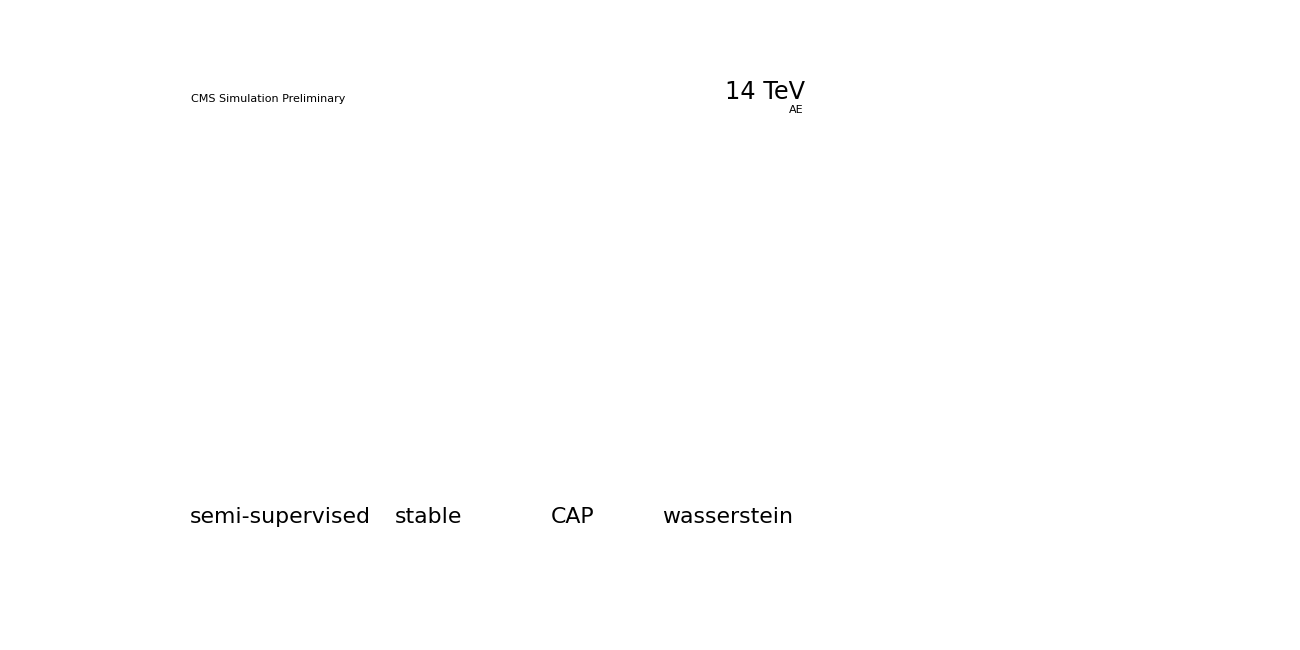

effs/ae_q99.svg

effs/ae_q99.pdf

effs/ae_q99.jpeg

```mathematica
(*Data AE q99*)
semisupervised={1.20,14.70,1.70,7.90,8.70,6.40,1.90,5.30,4.10,14.30};
CAP={0.60,2.20,0.40,2.30,0.70,2.90,0.30,3.20,1.70,1.70};
stable={1.20,10.30,0.80,4.60,6.50,3.90,1.10,3.60,2.80,11.60};
wasserstein={0.80,9.90,0.70,4.30,6.20,3.50,0.80,3.70,2.60,10.80};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "AE"]
Export["effs/" <> "ae_q99" <>".svg",plot,"SVG"]
Export["effs/" <> "ae_q99" <>".pdf",plot,"PDF"]
Export["effs/" <> "ae_q99" <>".jpeg",plot,"JPEG"]
```

## Efficiency Plot: VAE @ q99

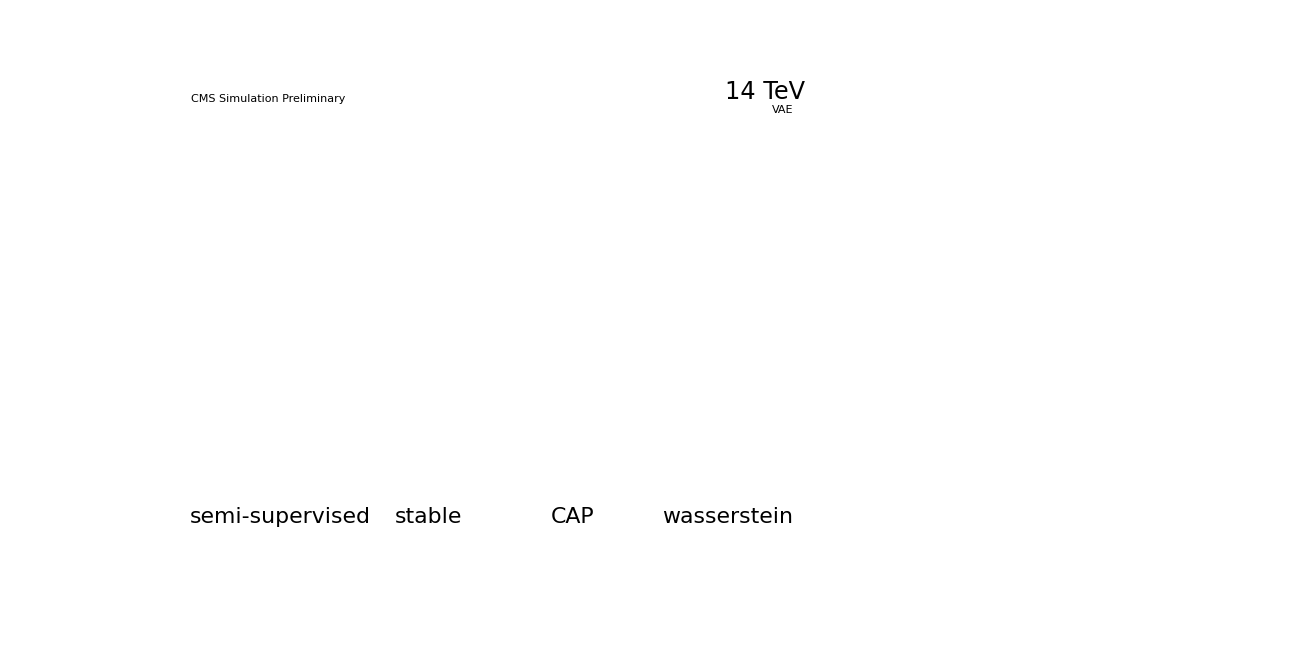

effs_cifar10/vae_q99.svg

effs_cifar10/vae_q99.pdf

effs_cifar10/vae_q99.jpeg

```mathematica
(*Data VAE q99*)
semisupervised={1.00,4.90,1.80,5.40,2.50,6.00,0.80,6.30,2.80,4.90};
CAP={0.20,0.60,0.20,1.20,0.20,1.10,0.80,2.50,0.90,0.30};
stable={1.20,0.00,0.20,0.00,0.00,0.00,0.00,0.00,0.30,0.00};
wasserstein={0.20,0.40,0.00,0.40,1.40,1.20,1.00,1.30,1.30,2.10};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17, "VAE",{0.63, 0.899}]
Export["effs_cifar10/" <> "vae_q99" <>".svg",plot,"SVG"]
Export["effs_cifar10/" <> "vae_q99" <>".pdf",plot,"PDF"]
Export["effs_cifar10/" <> "vae_q99" <>".jpeg",plot,"JPEG"]
```

```mathematica
"effs_cifar10/vae_q99.svg"
```

```mathematica
"effs_cifar10/vae_q99.pdf"
```

```mathematica
"effs_cifar10/vae_q99.jpeg"
```

## Efficiency Plot: SVDD @ q99

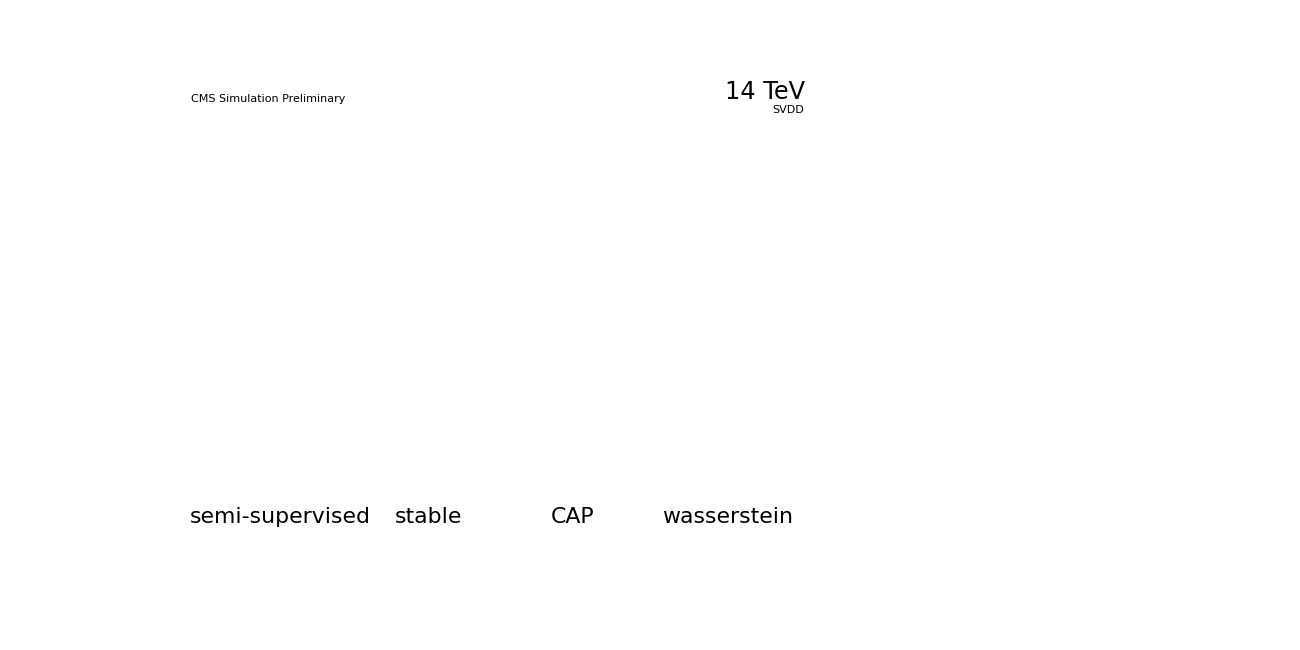

effs_cifar10/svdd_250Hz.svg

effs_cifar10/svdd_250Hz.pdf

effs_cifar10/svdd_250Hz.jpeg

```mathematica
(*Data SVDD*)
semisupervised={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.};
CAP={2.90,1.90,1.20,0.60,1.80,1.80,1.90,0.90,3.10,1.60};
stable={1.80,0.60,1.30,0.10,1.10,0.70,0.20,0.70,1.20,0.80};
wasserstein={0.,0.,0.,0.,0.,0.,0.,0.,0.,0.};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"SVDD", {0.639, 0.899}]
Export["effs_cifar10/" <> "svdd_250Hz" <>".svg",plot,"SVG"]
Export["effs_cifar10/" <> "svdd_250Hz" <>".pdf",plot,"PDF"]
Export["effs_cifar10/" <> "svdd_250Hz" <>".jpeg",plot,"JPEG"]
```

```mathematica
"effs_cifar10/svdd_250Hz.svg"
```

```mathematica
"effs_cifar10/svdd_250Hz.pdf"
```

```mathematica
"effs_cifar10/svdd_250Hz.jpeg"
```

## Efficiency Plot: RealNVP @ q99

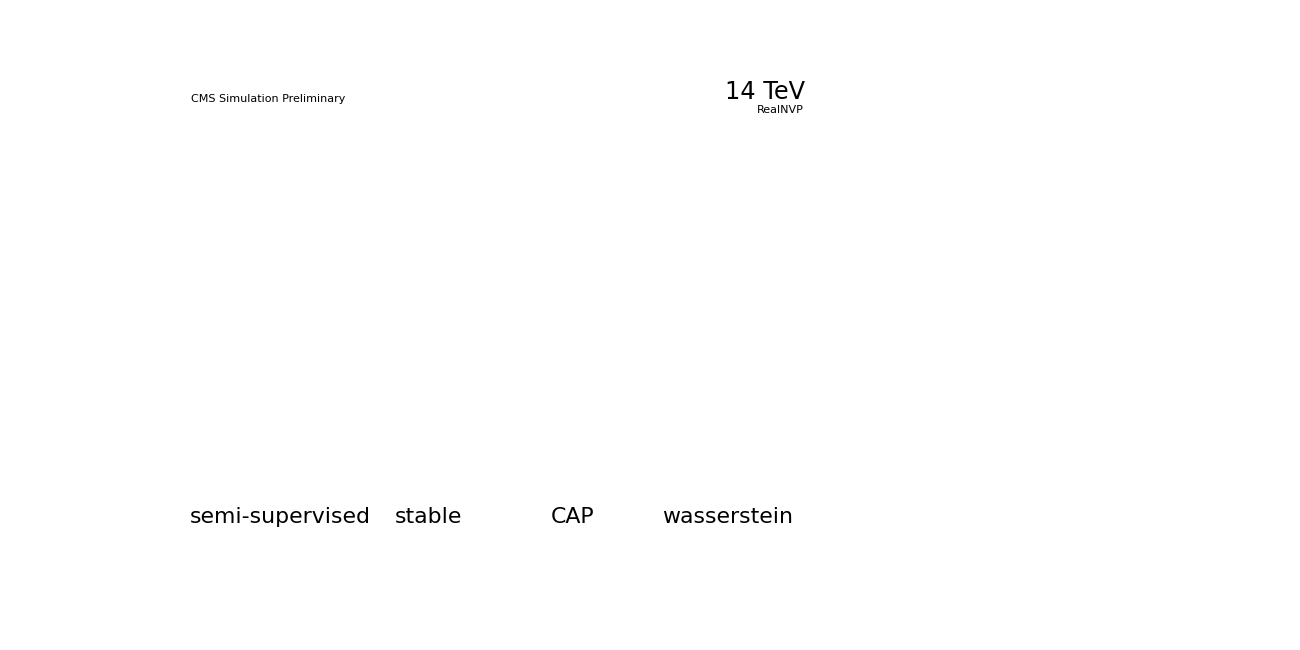

effs_cifar10/realnvp_250Hz.svg

effs_cifar10/realnvp_250Hz.pdf

effs_cifar10/realnvp_250Hz.jpeg

```mathematica
(*Data RealNVP*)
semisupervised={1.20,7.60,1.40,10.50,20.70,6.10,11.70,6.90,8.40,9.70};
CAP={1.60,5.60,1.10,6.00,8.50,5.40,5.10,4.90,4.70,5.80};
stable={0.60,2.80,1.10,3.80,6.90,3.60,4.40,2.80,3.80,3.50};
wasserstein={0.60,8.20,0.70,5.80,3.30,6.40,1.10,5.70,2.60,7.20};

plot = makeBoxCMS[{semisupervised,stable,CAP,wasserstein},{"semi-supervised","stable","CAP","wasserstein"},"Efficiency (%)",{0.085,0.9},{0.64,0.9},1,0.17,"RealNVP", {0.639, 0.899}]
Export["effs_cifar10/" <> "realnvp_250Hz" <>".svg",plot,"SVG"]
Export["effs_cifar10/" <> "realnvp_250Hz" <>".pdf",plot,"PDF"]
Export["effs_cifar10/" <> "realnvp_250Hz" <>".jpeg",plot,"JPEG"]
```

```mathematica
"effs_cifar10/realnvp_250Hz.svg"
```

```mathematica
"effs_cifar10/realnvp_250Hz.pdf"
```

```mathematica
"effs_cifar10/realnvp_250Hz.jpeg"
```